# Magnetic Field of a circular Ring

```mathematica
Capital Letter  = vector
X coordinate , ρ, α, β
R coordinate, r, θ, ϕ
```

```mathematica
(* with out lost of generality, R is on x-z plane *)
```

```mathematica
Element[{r,θ,ϕ,ρ,α,β},Reals]
```

(r|θ|ϕ|ρ|α|β)∈Reals

```mathematica
R= {r  Sin[θ],0,r  Cos[θ]};
X = {ρ Sin[α]Cos[β],ρ Sin[α]Sin[β],ρ  Cos[α]};
NORM2[X_,R_]:=(X[[1]]-R[[1]])^2+(X[[2]]-R[[2]])^2+(X[[3]]-R[[3]])^2
Collect[NORM2[X,R]//Expand//Simplify, r ρ]
```

r^2+ρ^2+r ρ (-2 Cos[α] Cos[θ]-2 Cos[β] Sin[α] Sin[θ])

```mathematica
B = ∇×A
```

```mathematica
A= μ/(4π)∫J[X]/Norm[R-X] ⅆX
```

```mathematica
jϕ=i/a DiracDelta[Cos[α]]DiracDelta[r-a];
```

```mathematica
J={-jϕ Sin[β],jϕ Cos[β],0};
```

```mathematica
(* by the cylindrical sysmmetry *)
(* Ay = Aϕ *)
Aϕ = μ/(4π)∫_0^r ∫_0^(2π) ∫_0^π (jϕ Cos[β])/((r^2+ρ^2+r ρ (-2 Cos[α] Cos[θ]-2 Cos[β] Sin[α] Sin[θ]))^(1/2))ρ^2 Sin[α]ⅆαⅆβⅆρ
```

```mathematica
Aϕ = μ/(4π)i/a∫_0^r ∫_0^(2π) ∫_0^π (DiracDelta[Cos[α]]DiracDelta[r-a]Cos[β])/((r^2+ρ^2+r ρ (-2 Cos[α] Cos[θ]-2 Cos[β] Sin[α] Sin[θ]))^(1/2))ρ^2 Sin[α]ⅆαⅆβⅆρ
```

```mathematica
(* The Cos[α] in DiracDelta give α=π/2*)
(* and ρ = a *)
Aϕ = (μ i a)/(4π)∫_0^(2π) Cos[β]/(√(r^2+a^2-2a r Cos[β] Sin[θ]))ⅆβ
```

```mathematica
∫_0^(2π) Cos[β]/(√(r^2+a^2-2a r Cos[β] Sin[θ]))ⅆβ
```

$Aborted

```mathematica
(* Integral is *)
k= (4 a r Sin[θ])/(r^2+a^2-2a r  Sin[θ]);
4/(√(r^2+a^2-2a r  Sin[θ]))(((2-k^2)EllipticK[k]-2 EllipticE[k])/k^2);
```

```mathematica
(* the B field is *)
B = {1/(r Sin[θ])D[Sin[θ] Aϕ,θ],-1/r D[ r Aϕ,r],0}
```

```mathematica
Aϕ=(μ i a)/(4π)4/(√(r^2+a^2-2a r  Sin[θ]))(((2-k^2)EllipticK[k]-2 EllipticE[k])/k^2);
```

```mathematica
(* Skipped a lot *)
(* For r < a *)
Br = (μ i a)/(2 r)Sum[((-1)^n(2n+1)!!)/(2^n n!)r^(2n+1)/a^(2n+2)LegendreP[2n+1,Cos[θ]],{n,0,∞}]
Bθ = (μ i a^2)/4 Sum[((-1)^n(2n+1)!!)/(2^n n!)(2n+2)/(2n+1)r^(2n)/a^(2n+3)LegendreP[2n+1,Cos[θ]],{n,0,∞}]
```

```mathematica
(* Fror r >a *)
Br = (μ i a)/(2 r)Sum[((-1)^n(2n+1)!!)/(2^n n!)a^(2n+1)/r^(2n+2)LegendreP[2n+1,Cos[θ]],{n,0,∞}]
Bθ =- (μ i a^2)/4 Sum[((-1)^n(2n+1)!!)/(2^n n!)a^(2n)/r^(2n+3)LegendreP[2n+1,Cos[θ]],{n,0,∞}]
```

```mathematica
√(( 1/(2 r)Sum[((-1)^n(2n+1)!!)/(2^n n!)r^(2n+1)/1 LegendreP[2n+1,Cos[θ]],{n,0,4}])^2+(1/4 Sum[((-1)^n(2n+1)!!)/(2^n n!)(2n+2)/(2n+1)r^(2n)/1 LegendreP[2n+1,Cos[θ]],{n,0,4}])^2)
```

```mathematica
√(1/16 (2 Cos[θ]-r^2 (-3 Cos[θ]+5 Cos[θ]^3)+9/32 r^4 (15 Cos[θ]-70 Cos[θ]^3+63 Cos[θ]^5)-5/32 r^6 (-35 Cos[θ]+315 Cos[θ]^3-693 Cos[θ]^5+429 Cos[θ]^7)+(175 r^8 (315 Cos[θ]-4620 Cos[θ]^3+18018 Cos[θ]^5-25740 Cos[θ]^7+12155 Cos[θ]^9))/8192)^2+1/(4 r^2)(r Cos[θ]-3/4 r^3 (-3 Cos[θ]+5 Cos[θ]^3)+15/64 r^5 (15 Cos[θ]-70 Cos[θ]^3+63 Cos[θ]^5)-35/256 r^7 (-35 Cos[θ]+315 Cos[θ]^3-693 Cos[θ]^5+429 Cos[θ]^7)+(315 r^9 (315 Cos[θ]-4620 Cos[θ]^3+18018 Cos[θ]^5-25740 Cos[θ]^7+12155 Cos[θ]^9))/16384)^2)/.{r-> √(x^2+y^2),Cos[θ]->y/(√(x^2+y^2))}
```

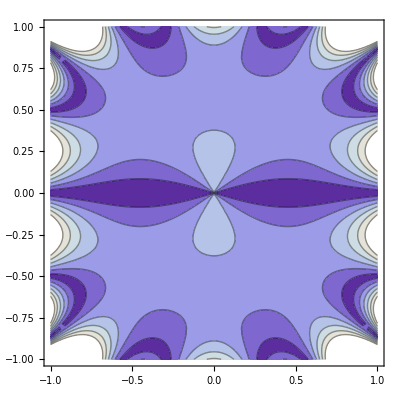

```mathematica
ContourPlot[√(1/16 ((2 y)/(√(x^2+y^2))-5/32 (x^2+y^2)^3 ((429 y^7)/((x^2+y^2)^(7/2))-(693 y^5)/((x^2+y^2)^(5/2))+(315 y^3)/((x^2+y^2)^(3/2))-(35 y)/(√(x^2+y^2)))-(x^2+y^2) ((5 y^3)/((x^2+y^2)^(3/2))-(3 y)/(√(x^2+y^2)))+9/32 (x^2+y^2)^2 ((63 y^5)/((x^2+y^2)^(5/2))-(70 y^3)/((x^2+y^2)^(3/2))+(15 y)/(√(x^2+y^2)))+(175 (x^2+y^2)^4 ((12155 y^9)/((x^2+y^2)^(9/2))-(25740 y^7)/((x^2+y^2)^(7/2))+(18018 y^5)/((x^2+y^2)^(5/2))-(4620 y^3)/((x^2+y^2)^(3/2))+(315 y)/(√(x^2+y^2))))/8192)^2+1/(4 (x^2+y^2))(y-35/256 (x^2+y^2)^(7/2) ((429 y^7)/((x^2+y^2)^(7/2))-(693 y^5)/((x^2+y^2)^(5/2))+(315 y^3)/((x^2+y^2)^(3/2))-(35 y)/(√(x^2+y^2)))-3/4 (x^2+y^2)^(3/2) ((5 y^3)/((x^2+y^2)^(3/2))-(3 y)/(√(x^2+y^2)))+15/64 (x^2+y^2)^(5/2) ((63 y^5)/((x^2+y^2)^(5/2))-(70 y^3)/((x^2+y^2)^(3/2))+(15 y)/(√(x^2+y^2)))+(315 (x^2+y^2)^(9/2) ((12155 y^9)/((x^2+y^2)^(9/2))-(25740 y^7)/((x^2+y^2)^(7/2))+(18018 y^5)/((x^2+y^2)^(5/2))-(4620 y^3)/((x^2+y^2)^(3/2))+(315 y)/(√(x^2+y^2))))/16384)^2),{x,-1,1},{y,-1,1}]
```